```mathematica
arad
```

7.56683×10^-15

```mathematica
r0=5*10^6
r1=3*10^7
rho0=7*10^8
rho1=4*10^8
T0=3*10^10
T1=10^(10)
```

5000000

30000000

700000000

400000000

30000000000

10000000000

```mathematica
r1/rl
```

67.7252

```mathematica
r1*1.
```

3.×10^7

```mathematica
100*rl
```

4.42966×10^7

```mathematica
omegak=Sqrt[G*M/r^3]
tauk=2*Pi/omegak
tauorbitr1=tauk//.{r->r1}
```

1.99529×10^13 √(1/r^3)

(3.14901×10^-13)/(√(1/r^3))

0.0517435

```mathematica
rho=(rho1-rho0)/(r1-r0)*(r-r0)+rho0
T=(T1-T0)/(r1-r0)*(r-r0)+T0
qrad=9.2*10^(33)*(T/10^11)^6*(rho/10^(10))
```

700000000-12 (-5000000+r)

30000000000-800 (-5000000+r)

9.2×10^-43 (30000000000-800 (-5000000+r))^6 (700000000-12 (-5000000+r))

```mathematica
urad=11/12*arad*T^4
taurad=urad/qrad
```

6.93626×10^-15 (30000000000-800 (-5000000+r))^4

(7.53942×10^27)/((30000000000-800 (-5000000+r))^2 (700000000-12 (-5000000+r)))

```mathematica
M=3*msun
rl=G*M/c^2
tl=rl/c
taurat=taurad/tl
```

5.967×10^33

442966.

0.0000147758

(5.10256×10^32)/((30000000000-800 (-5000000+r))^2 (700000000-12 (-5000000+r)))

```mathematica
tl*10^6
```

14.7758

```mathematica
tauorbitr1/tl
```

3501.92

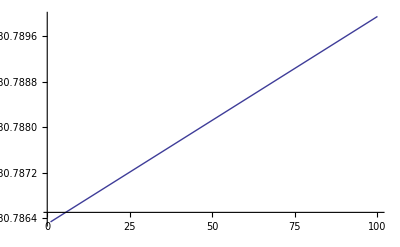

```mathematica
Plot[taurat,{r,1,100}]
```

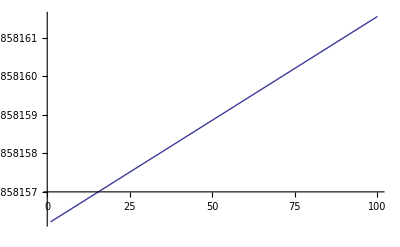

```mathematica
Plot[taurad,{r,1,100}]
```

```mathematica
256*48
```

12288